```mathematica
transmissions=Table[Import["~/Downloads/PhD_new/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[x]<>".dat"],{x,Range[1,100,2]}]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=SparseArray[{{i_,i_}->ω+I*δ-ϵ,{i_,j_}/;Abs[i-j]==1->t},{m,m}]
```

```mathematica
Tagnrin[t_,m_]:=SparseArray[Table[{i,i},{i,Range[1,m,2]}]->t,{m,m}]
```

```mathematica
Tagnrcon[t_,m_]:=SparseArray[Table[{i,i},{i,Range[2,m,2]}]->t,{m,m}]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,γ_]:=LEFT[ω,δ,t,ϵ,γ]=Module[{},J=Inverse[β[ω,δ,t,ϵ,γ]];B=Inverse[β[ω,δ,t,ϵ,γ]];T=Tagnrin[1,γ];Do[J=PseudoInverse[IdentityMatrix[γ]-B.T.J.T].B,50000];J]
```

```mathematica
Monitor[Table[-Im[LEFT[w,0.0001,1,0,5][[1,1]]],{w,Range[0,3,0.01]}],w]
```

{0.337894,0.329462,0.335652,0.333331,0.3308,0.337507,0.329038,0.335097,0.334865,0.328692,0.335827,0.334978,0.328511,0.331859,0.336866,0.334596,0.329772,0.327813,0.328614,0.330096,0.330933,0.330709,0.329399,0.327501,0.326918,0.330333,0.33479,0.330105,0.32675,0.334133,0.325587,0.333587,0.325441,0.329469,0.332516,0.328029,0.324828,0.323898,0.323782,0.325052,0.329098,0.330248,0.420306,0.487904,0.521714,0.559992,0.582603,0.600575,0.618657,0.635289,0.652003,0.669751,0.677012,0.689045,0.695983,0.710203,0.717876,0.724574,0.732304,0.736732,0.737535,0.749365,0.748965,0.752333,0.757398,0.760265,0.764732,0.772803,0.769933,0.774796,0.779596,0.781182,0.779753,0.784662,0.783892,0.78937,0.791215,0.790948,0.788183,0.794422,0.79271,0.792354,0.795164,0.795208,0.795045,0.792829,0.793267,0.796769,0.793617,0.796776,0.796646,0.793402,0.795263,0.792028,0.791737,0.794376,0.790076,0.79025,0.788599,0.791365,0.790078,0.820179,0.834416,0.841602,0.848598,0.855819,0.859304,0.863655,0.867873,0.871368,0.874216,0.87404,0.876587,0.877998,0.880536,0.881542,0.882893,0.882915,0.885196,0.885039,0.885581,0.884764,0.885477,0.884067,0.884508,0.883014,0.88268,0.881654,0.881059,0.879494,0.880158,0.878667,0.876578,0.875612,0.873754,0.872072,0.87007,0.86843,0.866762,0.864705,0.862498,0.86049,0.857693,0.855701,0.853027,0.850451,0.847764,0.844654,0.842069,0.839773,0.836256,0.833236,0.830059,0.82634,0.82369,0.820175,0.816208,0.813059,0.808851,0.805661,0.801882,0.797459,0.793377,0.789416,0.785532,0.780633,0.776556,0.772162,0.767371,0.762385,0.757575,0.752637,0.747666,0.742381,0.737085,0.732108,0.72645,0.720871,0.715112,0.709144,0.703123,0.696761,0.69046,0.683597,0.676927,0.670003,0.662907,0.655669,0.647918,0.640113,0.631899,0.623478,0.614598,0.605293,0.595433,0.584856,0.573542,0.560977,0.546671,0.52924,0.494409,0.488254,0.484152,0.480077,0.475845,0.471525,0.467192,0.462724,0.458265,0.453649,0.448931,0.444097,0.439181,0.434098,0.428948,0.423765,0.418354,0.412803,0.407201,0.401451,0.395511,0.389408,0.38315,0.376693,0.369981,0.363197,0.356056,0.348705,0.341118,0.333245,0.324963,0.316323,0.307305,0.297683,0.287535,0.276733,0.264969,0.252159,0.237761,0.221172,0.20074,0.170523,0.134871,0.133793,0.132804,0.131815,0.130833,0.12984,0.128809,0.127757,0.126736,0.125639,0.12457,0.123467,0.122325,0.121203,0.12002,0.118844,0.11764,0.116406,0.115167,0.113892,0.112594,0.111276,0.109923,0.108552,0.107147,0.105722,0.10426,0.102769,0.101244,0.0996888,0.0980967,0.0964696,0.0948014,0.0930923,0.0913408,0.0895437,0.0876983,0.0858016,0.0838502,0.0818396,0.0797662,0.0776246,0.0754093,0.0731134,0.0707293,0.0682477,0.0656576,0.0629457,0.0600956,0.0570866,0.0538923,0.0504774,0.0467938,0.0427721,0.0383062,0.0332174,0.0271577,0.0192302,0.00136965}

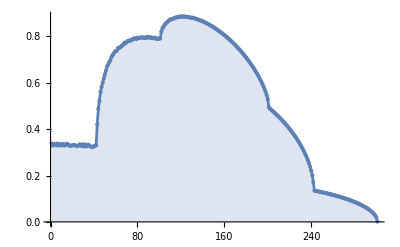

```mathematica
ListPlot[%59,Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
ListPlot[%53,Filling->Axis,Mesh->All,Joined->True]
```